```mathematica
(* An rblock is bad: a disease *)
(* An rblock passes software verification: a test *)
(* An rblock passes fraud proof: a second test *)

(* Probability an rblock fails given it passes software verification *)
R =1-10^(-15);

(* Withdraw amount ETH *)
S$0=100;
(* Carrying costs *)
U=0;
(* Gas costs *)
DD=0.008;
(* APY on ETH *)
r=0.2;
(* APY on ETHxx *)
y=0;
(* Dispute period (in years) *)
dt=0.0164;

(* Price *)
F$0=(S$0+U-DD)Exp[(y-r)*dt]*R//N
```

99.6646

```mathematica
fff[sss_,ddd_,rrr_,RRR_]=(sss-ddd)Exp[(-rrr)*dt]*RRR;
fff[100,0.008,0.2,1-10^(-15)]
fff[0.05,0.008,0.2,1-10^(-15)]
```

99.6646

0.0418625

## Chart 1: R

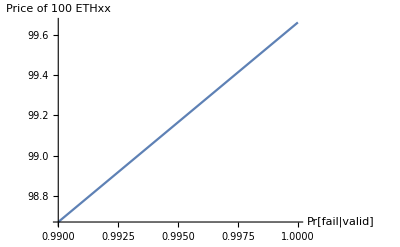

```mathematica
Plot[fff[100,0.008,0.2,x],{x,0.99,1},AxesLabel->{"Pr[fail|valid]","Price of 100 ETHxx"},ImageSize->400]
Export[NotebookDirectory[]<>"chart1.pdf",%];
```

## Chart 2: s0

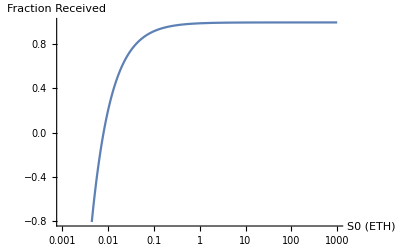

```mathematica
LogLinearPlot[{fff[x,0.008,0.2,1-10^(-15)]}/x,{x,0.001,1000},AxesLabel->{"S0 (ETH)","Fraction Received"},ImageSize->400]
Export[NotebookDirectory[]<>"chart2.pdf",%];
```